```mathematica
f= NDSolve[{y'[t]==t*Exp[3*y[t]]-2*y[t],y[0]==0},y[t],{t,0,1}]
```

NDSolve::ndsz: At t == 0.955942, step size is effectively zero; singularity or stiff system suspected.

{{y[t]→InterpolatingFunction[…][t]}}

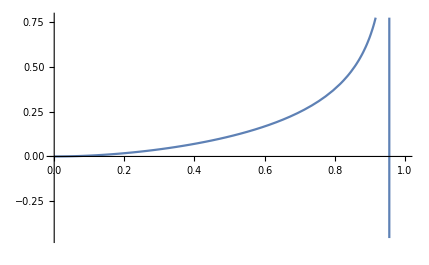

```mathematica
Plot[Evaluate[{y[t]} /.f],{t,0,1}]
```

```mathematica
g= NDSolve[{y'[t]==1-(t-y[t])^2,y[2]==0},y[t],{t,2,3}]
```

NDSolve::ndsz: At t == 2.5, step size is effectively zero; singularity or stiff system suspected.

{{y[t]→InterpolatingFunction[…][t]}}

```mathematica
Plot[Evaluate[{y[t]} /.g],{t,2,3}]
```

-Graphics-

```mathematica
h= NDSolve[{y'[t]==1+y[t]/t,y[1]==2},y[t],{t,1,2}]
```

{{y[t]→InterpolatingFunction[…][t]}}

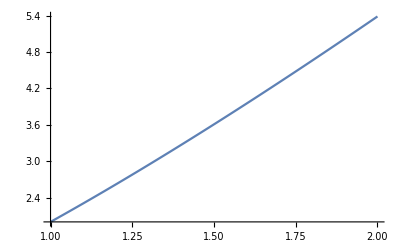

```mathematica
Plot[Evaluate[{y[t]} /.h],{t,1,2}]
```

```mathematica
i= NDSolve[{y'[t]==Cos[2*t]+Sin[3*t],y[0]==1},y[t],{t,0,1}]
```

{{y[t]→InterpolatingFunction[…][t]}}

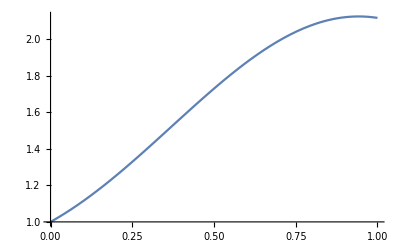

```mathematica
Plot[Evaluate[{y[t]} /.i],{t,0,1}]
```